## Calculating the Increase in Temperature of the Isocyanate Stream Assuming Complete Reaction with Polyol

Key properties (assuming MDI isocyanate)

```mathematica
ΔHrxn = -24000*4.184; (* heat of reaction of R-NCO + OH in kJ/mol *)
nNCO = 2; (* number of NCO groups per molecule *)
ρIso = 1230; (* density of MDI, kg/m^3 *)
ρPoly = 1018; (* density of VORANOL 4701 polyol, kg/m^3 *)
Mw = .286; (* molecular weight of MDI, kg/mol *)
L = 0.1; (* length of channel, m; note that ΔT is independent of L in this calculation *)
τ = 0.1; (* length of experiment, s *)
RIso = 1*^-5; (* radius of isocyanate stream, m *)
RPoly = 25*^-5; (* radius of liquid stream including polyol, m *)
cpIso= 430*4.184; (* specific heat of MDI, J/kg.C *)
cpPoly = 497*4.184; (* specific heat of VORANOL 4701 at 20C, J/kg.C*)
kPoly = 0.126; (* W/m.K *)
kIso = 0.0003 *4.184*100; (* MDI thermal conductivity, W/m.K, https://dowac.custhelp.com/app/answers/detail/a_id/5537 *)
vMean = 0.5; (* mean velocity, m/s *)
```

Distance that heat diffuses in polyol over the course of the experiment

```mathematica
αPoly = kPoly/(ρPoly cpPoly); (* thermal diffusivity of polyol, m^2/s*)
dPoly = Sqrt[αPoly τ] (* distance that heat travels during experiment into polyol, m *)
```

0.0000771503

Distance that reacting interface travels (into isocyanate) according to result of Machuga et al 1988

```mathematica
vInterface = 3*^-4; (* velocity of interface, m/s *)
dInterface = vInterface*τ (* distance that interface travels during experiment, m*)
```

0.00003

Change in temperature assuming uniform heating of entire tube

```mathematica
VIso = π RIso^2 L;
VPoly = π (RPoly^2 - RIso^2) L;
mIso = ρIso VIso;
mPoly= ρPoly VPoly;
nMol = mIso / Mw;
q = -ΔHrxn*nMol; (* heat released *)
ΔT = q/((mIso cpIso) + (mPoly cpPoly)) (* rise in temperature in degrees C *)
```

0.326388

Change in temperature assuming uniform heating of isocyanate only

```mathematica
ΔT = q/(mIso cpIso)  (* rise in temperature in degrees C *)
```

195.154

Change in temperature assuming heat only reaches distance traveled by diffusion + interfacial motion

```mathematica
dHeat = dPoly +dInterface;
RHeat = RIso + dHeat;
VHeatPoly = π (RHeat^2 -RIso^2)*L;
mHeatPoly =ρPoly VHeatPoly;
ΔT = q/((mIso cpIso) +(mHeatPoly cpPoly))
```

1.48599

Change in temperature assuming heat only reaches distance traveled by thermal diffusion

```mathematica
dHeat = dPoly;
RHeat = RIso + dHeat;
VHeatPoly = π (RHeat^2 -RIso^2)*L;
mHeatPoly =ρPoly VHeatPoly;
ΔT = q/((mIso cpIso) +(mHeatPoly cpPoly))
```

2.68441

Assume gaussian distribution of heat (as in diffusion model) with distribution width equal to the thermal diffusion length + the radius of the isocyanate stream

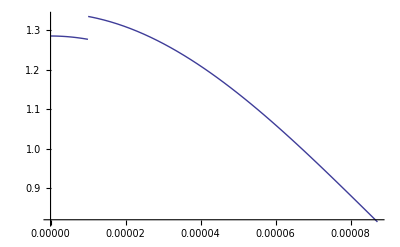

```mathematica
A = q /(2π Integrate[Exp[-r^2/(2RHeat^2)]r,{r,0,∞}]L);
qDensity[r_]:= A Exp[-r^2/(2RHeat^2)];
ΔTfn[r_]:=qDensity[r]/(ρIso cpIso HeavisideTheta[RIso-r]+ρPoly cpPoly HeavisideTheta[r-RIso]);
Plot[ΔTfn[r],{r,0,RHeat}]
```

```mathematica
Integrate[2π qDensity[r]r,{r,0,∞}]L
```

0.000324265

```mathematica
q
```

0.00324265

## Modeling Heat Transfer in Steady-state Forced Convection through Insulated Pipe with Uniform Heat Generation (Poppendiek and Palmer, 1952)

Assume all heat is kept in isocyanate stream

```mathematica
VIso = π RIso^2 L;
mIso = ρIso VIso;
nMol = mIso/ Mw ;
q = -ΔHrxn*nMol*nNCO; (* heat released *)
qDot = q/(VIso τ); (* heat generation density per time *)
ΔT =  qDot/(2vMean ρIso cpIso)L(* assume full reaction by the time the fluid exits the tube *)
```

390.307

Assume that heat generated in isocyanate stream only

```mathematica
ΔT = qDot RIso^2 L/(2 ρIso cpIso vMean RIso^2 + ρPoly cpPoly vMean (RPoly^2-RIso^2))
```

1.30337

```mathematica
(qDot RIso^2 (cpIso RIso^4 ρIso+2 cpPoly RPoly^2 (-RIso^2+RPoly^2) ρPoly))/(8 kIso RPoly^2 (2 cpIso RIso^2 ρIso+cpPoly (-RIso^2+RPoly^2) ρPoly))
```

1.71454

```mathematica
(cpPoly qDot RIso^2 ρPoly (RIso^4-4 RIso^2 RPoly^2+3 RPoly^4+4 (RIso^4-RIso^2 RPoly^2-RPoly^4) Log[RPoly/RIso]))/(8 kPoly RPoly^2 (2 cpIso RIso^2 ρIso+cpPoly (-RIso^2+RPoly^2) ρPoly))
```

-8.47028

```mathematica
Exp[0.001]
```

1.001

```mathematica
Bo = 3000*1800*0.000025/(5.67*^-8*300^3)
```

88.1834

```mathematica
1500*0.02/(4*5.67*^-8*300^3)
```

4.89908

```mathematica
1*^5
```

100000